```mathematica
"Multipole Single U - UHF-Uniform Heat Flux"
```

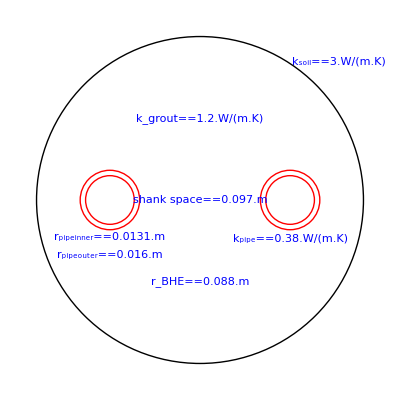

```mathematica
rhof=988.04 (*fluid density[kg/m^3]*); Qi= 0.000266 (*flow-rate[m^3/s]*); rpi=0.0131 (*inner radius[m]*); mu=0.0005465 (*dynamic viscosity [Pa.s]*); cpf=4182 (*fluid specificheat capacity [J/kgK]*); kfluid=0.64 (*fluid thermal conductivity [W/(m.K)]*); kpipe=0.38 (*pipe thermal conductivity [W/(m.K)]*); rpo=0.016 (*outer radius of pipe [m]*); kgrout=1.2 (*grout thermal conductivity [W/(m.K)]*); ss=0.097 (*shank space [m]*); rb=0.088(*borehole radius [m]*); ks=3 (*ground thermal conductivity [W/(m.K)]*);Hb=50 (*Borehole depth [m]*);
Graphics[{Circle[{0,0},rb],{Red,Circle[{-ss/2,0},rpo],Circle[{ss/2,0},rpo],Circle[{ss/2,0},rpi],Circle[{-ss/2,0},rpi]},{Blue,Inset[Subscript[k, grout]==kgrout .(W/(m.K)),{0,rb/2}],Inset[Subscript[k, soil]==ks .(W/(m.K)),{rb*0.85,rb*0.85}],Inset[Subscript[k, pipe]==kpipe .(W/(m.K)),{ss/2,-rpo*1.3}],Inset[Subscript[r, pipeinner]==rpi .(m),{-ss/2,-rpi*1.5}],Inset[Subscript[r, pipeouter]==rpo .(m),{-ss/2,-rpi*1.5-0.01}],Inset[shank space==ss .(m),{0,0}],Inset[Subscript[r, BHE]==rb .(m),{0,-rb/2}]}}]
```

```mathematica
Which[ss/2+rpo>rb,"out of range"];
Vfluid[Qi_,rpi_]:=Qi/(π*rpi^2);
θ1[ss_,rb_]:=ss/(2*rb);
θ2[rb_,rpo_]:=rb/rpo;
θ3[rpo_,ss_]:=rpo/ss;
σ1[kgrout_,ks_]:=(kgrout-ks)/(kgrout+ks);
Rpc[kpipe_,rpo_,rpi_]:=1/(2*π*kpipe)*Log[rpo/rpi];
Re1[rhof_,Qi_,rpi_,mu_]:=(rhof*Vfluid[Qi,rpi]*2*rpi)/mu;
Pr[kfluid_,cpf_,mu_]:=(cpf*mu)/kfluid;
ff[rhof_,Qi_,rpi_,mu_]:=(0.79*Log[Re1[rhof,Qi,rpi,mu]]-1.64)^-2;
NUpi[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_]:=((ff[rhof,Qi,rpi,mu]/8)*(Re1[rhof,Qi,rpi,mu]-1000)*Pr[kfluid,cpf,mu])/(1+12.7*(ff[rhof,Qi,rpi,mu]/8)^(1/2)*(Pr[kfluid,cpf,mu]^(2/3)-1)) ; 
hpi[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_]:=(NUpi[rhof,Qi,rpi,mu,cpf,kfluid]*kfluid)/(2*rpi) ; 
Rpic[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_]:=1/(2*π*rpi*hpi[rhof,Qi,rpi,mu,cpf,kfluid]) ; 
Rp[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_,kpipe_,rpo_]:=Rpc[kpipe,rpo,rpi]+Rpic[rhof,Qi,rpi,mu,cpf,kfluid];
Beta1[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_,kpipe_,rpo_,kgrout_]:=2*π*kgrout*Rp[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo];
Rb1U[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_,kpipe_,rpo_,kgrout_,ss_,rb_,ks_]:=1/(4*π*kgrout)(Beta1[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout]+Log[θ2[rb,rpo]/(2*θ1[ss,rb]*(1-θ1[ss,rb]^4)^σ1[kgrout,ks])]-(θ3[rpo,ss]^2*(1-(4*σ1[kgrout,ks]*θ1[ss,rb]^4)/(1-θ1[ss,rb]^4))^2)/((1+Beta1[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout])/(1-Beta1[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout])+θ3[rpo,ss]^2*(1+(16*σ1[kgrout,ks]*θ1[ss,rb]^4)/((1-θ1[ss,rb]^4)^2)))) ;
Ra1U[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_,kpipe_,rpo_,kgrout_,ss_,rb_,ks_,Hb_]:=1/(π*kgrout)*(Beta1[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout]+Log[((1+θ1[ss,rb]^2)^σ1[kgrout,ks])/(θ3[rpo,ss]*(1-θ1[ss,rb]^2)^σ1[kgrout,ks])]-(θ3[rpo,ss]^2*(1-θ1[ss,rb]^4+4*σ1[kgrout,ks]*θ1[ss,rb]^2)^2)/((1+Beta1[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout])/(1-Beta1[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout])*(1-θ1[ss,rb]^4)^2-θ3[rpo,ss]^2*(1-θ1[ss,rb]^4)^2+8*σ1[kgrout,ks]^2*θ1[ss,rb]^2*θ3[rpo,ss]^2*(1+θ1[ss,rb]^4)));
Rbstar[rhof_,Qi_,rpi_,mu_,cpf_,kfluid_,kpipe_,rpo_,kgrout_,ss_,rb_,ks_,Hb_]:=Rb1U[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout,ss,rb,ks]+1/(3*Ra1U[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout,ss,rb,ks,Hb])*(Hb/(rhof*cpf*Vfluid[Qi,rpi]))^2
```

```mathematica
Rbstar[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout,ss,rb,ks,Hb]
```

0.147144

```mathematica
Manipulate[Rbstar[rhof,Qi,rpi,mu,cpf,kfluid,kpipe,rpo,kgrout,ss,rb,ks,Hb],{Qi,0.0001,0.0005},{kpipe,0.3,3},{kgrout,0.5,4},{Hb,40,200},{ks,0.5,7},{rhof,900,1100},{rpi,0.01,0.02},{ss,0.05,0.1},{rb,0.05,0.15}]
```

```mathematica
Rbstar[988.04,0.000266,0.0131,0.0005465,4182,0.64,0.38,0.016,1.2,0.097,0.088,3,50]
```

0.147144